```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
l=Flatten @ Import["test2-add.dat"];
```

```mathematica
len=Length[l]
1./Sqrt[len]
```

65536

0.00390625

```mathematica
Mean[l]
StandardDeviation[l]
```

1.36517

94.0293

{1.,0.999943,0.999801,0.999587,0.999307,0.998965,0.998566,0.998113,0.997608,0.997054,0.996452,0.995805,0.995114,0.99438,0.993605,0.99279,0.991935,0.991043,0.990114,0.989148,0.988148}

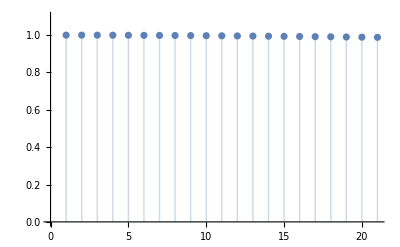

20.9075

```mathematica
cf=CorrelationFunction[l,{20}]
ListPlot[cf,Filling->0,PlotRange->{0,1.1}]
Total[cf]
```

```mathematica
(* Allan variance estimate *)
diffs=Most[l]-Rest[l];
sqdiffs=diffs^2;
sumsqdiffs=Total[sqdiffs];
avar=sumsqdiffs/(2len)
adev=Sqrt[avar]
```

0.499999

0.707106

```mathematica
(* Convert to integers *)
lint=N@Round[l];
Mean[lint]
StandardDeviation[lint]
```

1.36623

94.0299

```mathematica
(* Allan variance estimate *)
diffs=Most[lint]-Rest[lint];
sqdiffs=diffs^2;
sumsqdiffs=Total[sqdiffs];
avar=sumsqdiffs/(2len)
adev=Sqrt[avar]
```

0.583679

0.763989

{1.,0.999934,0.999792,0.999578,0.999297,0.998956,0.998557,0.998104,0.997599,0.997045,0.996443,0.995796,0.995105,0.994371,0.993596,0.99278,0.991926,0.991034,0.990105,0.989139,0.988139}

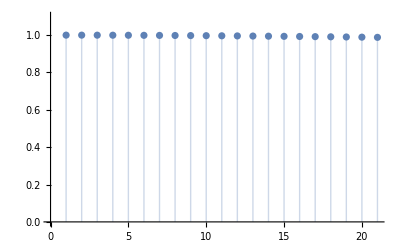

20.9073

```mathematica
cf=CorrelationFunction[N[lint],{20}]
ListPlot[cf,Filling->0,PlotRange->{0,1.1}]
Total[cf]
```

0.

{a→329.732,x0→-4.9966,σ→73.0572}

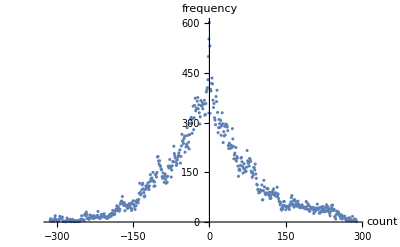

```mathematica
(* Distribution *)
ta=Tally[lint];
x0est=Sort[ta,#1[[2]]>#2[[2]]&][[1,1]]
p1=ListPlot[ta,AxesLabel->{"count","frequency"},LabelStyle->Larger];
fnc=a Exp[-(x-x0)^2/(2σ^2)];
sol=FindFit[ta,fnc,{{a,20000},{x0,x0est},{σ,1}},x]
fnc=fnc/.sol;
p2=Plot[fnc,{x,-4,4},PlotRange->All];
pp=Show[p1,p2]
```

0.998256

{1.,0.00363716,0.000916309,0.00968221,0.000198466,-0.002181,0.00396348,0.000720011,0.00319814,-0.000712818,-0.00117344,0.00176414,0.000756659,-0.0030927,0.00104398,0.00280973,0.00060599,-0.000210087,0.000260316,-0.00492004,0.00658658}

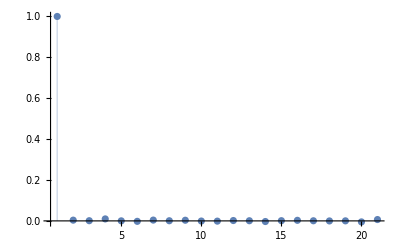

1.02385

```mathematica
(* LSB correlations *)
l2=Map[Mod[#,2]&,l];
Mean[l2]
cf=CorrelationFunction[l2,{20}]
ListPlot[cf,Filling->0,PlotRange->All]
Total[cf]
```